Big Data Homework 2

```mathematica
Name : Hao Liu
NetID : hl1283
```

Problem 1

(a)
The role of the sparsity criterion forces algorithm to find the sparsest representation of input, with least non-zero entries. Here using L_1norm to approximate the L_0norm, which is the number of non-zero entries.

(b)
1.L_0 is hard to optimize, because it's not convex and its gradient has no use in gradient descend methods, always zero. L_1 is convex and easy to optimize.
2.Although L_1is not the best approximation to L_0, in [1] it is showed that Lasso(L_1) tends to make many coefficients become zero. 

[1]Tibshirani. Regression Shrinkage and Selection via the Lasso. Journal of the Royal Statistical Society, Ser. B, 58(1):267{288, 1996.

Problem 2

(a)
∇_y_k E(W,x,y_k)=-2 W^T x+2 W^T W y_k      +      λ sgn(y_k)
Note: According to Amir Beck and Marc Teboulle’s paper, in the step(3) we should use ∇_y_k (||x-W y_k(||)_2^2) instead of ∇_y_k E.
(b)
L=2λ_max(W^T W), because
		 sup_(y_k,(ỹ)_k) (||Δ_y_k f(W,x,y_k)-Δ_y_k f(W,x,(ỹ)_k)||)/(||y_k-(ỹ)_k||)=sup_(y_k,(ỹ)_k) (2||W^T W(y_k-(ỹ)_k)||)/(||y_k-(ỹ)_k||)=2ρ(W^T W)=2λ_max(W^T W)
in which ρ(·) is spectral radius.
(c) 
Intuitively, it will make all entry z_i that -α<z_i<α becone zero. So small elements in z become 0, so make z sparse in an intuitive way.

Mathematically, in [2] it is showed that (2.6) 
-Graphics-
and 
from (2.3) we know 
		    -Graphics-
			-Graphics-

[2] Amir Beck and Marc Teboulle. A fast iterative shrinkage-thresholding algorithm for linear inverse problems. SIAM J. Img. Sci., 2(1):183￿02, March 2009.


(d) In k-th step, given the search step Lstep, we do
	step = 0
	while E(W,x,p_L(y_k))≥Q_L(p_L(y_k),y_k) and step <max_backsearch_step do
		L = L / Lstep
		step = step + 1
	end

(e)We set A=W^TW, (L̂)_k=2*λ_(max in k step)(A)
Question: Actually L doesn’t change in the FISTA algorithm, why we must update it each step and why compute it in the first step for a pretty good convergence and then use it in the following steps, it works in my experiments.

Problem 3

(a) ∇_W E(W,x,z)=-2 W^T x+2 W^T W z and (∇_W E(W,x,z))_(i,j)=(∂E(W,x,z))/(∂W_(i,j))=-2 x_i z_j+2∑_(k=1)^m w_ik z_k z_j.
Where W is n×m matrix and x=(x_1,x_2,...,x_n)^T, z=(z_1,z_2,...,z_m)^T.

(b) Yes, there is a way. For the dataset X={x_1,x_2,...,x_n}, we want to minimize
			Loss=∑_(k=1)^m ||x_k-W z_k(||)_2^2
which is equivalent to minimize
			||(x_1,x_2,...,x_n)-W (z_1,z_2,...,z_n)(||)_F^2
which is equivalent to solve
		W (z_1,z_2,...,z_n)(z_1,z_2,...,z_n)^T=(x_1,x_2,...,x_n)(z_1,z_2,...,z_n)^T
So when n is big enough and let 
		A = (z_1,z_2,...,z_n)(z_1,z_2,...,z_n)^T = ∑_(k=1)^n z_k z_k^T
		B = (x_1,x_2,...,x_n)(z_1,z_2,...,z_n)^T = ∑_(k=1)^n x_k z_k^T
then
				W=B A^-1

(c)(d) Following is the results from different λ = 2, 0.5, 0.005.
We find that when λ is big the obtained  strocks are long.

λ=2

λ=0.5

λ=0.005

(e) It doen’t work at all. I implement it in this way:
First a few steps, do gradient descent. And then do directly solution. And each step we update matrix A and B.
Explanation: 
     In the direct solution, we need z_kis accurate. But when W is not accurate z_kis far from accurate.

Problem 4

(a)We can use three steps alternating direction 
PSD(X={x_1,x_2,...,x_m})
1 Initialize W_0 in random
2 for k = 1 to K (or convergence test)
3	Get an input x_k∈X
4	z_k = FISTA(x_k,W_(k-1))
5	W_k=W_(k-1)-η_k·∇_(W_(k-1)) E(W_(k-1),x_k,z_k, V_(k-1))
6	Normalize the columns of W_kto norm 1
7	V_k = V_(k-1)-η_k·∇_(V_(k-1)) E(W_k,x_k,z_k, V_(k-1))
Or
We can use two steps alternating direction 
PSD(X={x_1,x_2,...,x_m})
1 Initialize W_0 in random
2 for k = 1 to K (or convergence test)
3	Get an input x_k∈X
4	z_k = FISTA(x_k,W_(k-1))
5	W_k=W_(k-1)-η_k·∇_(W_(k-1)) E(W_(k-1),x_k,z_k, V_(k-1))
6	Normalize the columns of W_kto norm 1
7	V_k = V_(k-1)-η_k·∇_(V_(k-1)) E(W_(k-1),x_k,z_k, V_(k-1))

(b)(c)(d)
Softplus and Positive are both to model rectiﬁed linear units. And we can see in following figure that they are very similar.
Note: The patches are preprocessed by local contrast normalization algorithm with gauss filter of size 5, which helps a lot.

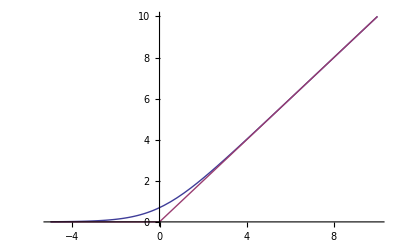

```mathematica
Plot[{Log[1+Exp[x]],Max[x,0]},{x,-5,10}]
```

Following are the visulization results from Softplus:

Remark: The normalization problem(each update normalize the dictionary) was pointed out by discussing with Siyuan Zhou.

## Channel Y:

torch PSD.lua - lambda 0.6 - eta 0.1 - decay 0.1 - maxiter 100000

                    Decoder                                        Encoder

```mathematica
-Graphics--Graphics-
```

## Channel U:

torch PSD.lua - lambda 0.4 - eta 0.1 - decay 1 - maxiter 100000 - channel 2

                    Decoder                                        Encoder

```mathematica
-Graphics--Graphics-
```

## Channel V:

torch PSD.lua - lambda 1 - eta 0.1 - decay 1 - maxiter 100000 - channel 3

                    Decoder                                        Encoder

```mathematica
-Graphics--Graphics-
```

Following are the Training Error results from Softplus:

Channel Y                                                      Channel V (U is similar)

```mathematica
-Graphics--Graphics-
```

Following are the Training Error results from Positive:

Channel Y                                                      Channel V (U is similar)

```mathematica
-Graphics--Graphics-
```

Remark: The error figures above show there is no big diffrence between Softplus and Positive.